```mathematica
By Le Chen.
Crated on Mon 01 Nov 2021 09:55:00 PM CDT
```

```mathematica
t Sum[((-ν/2 t^2 x^α)^k)/Gamma[2 k+2],{k,0,∞}]
```

(√2 x^(-α/2) Sin[(t x^(α/2) √ν)/(√2)])/(√ν)

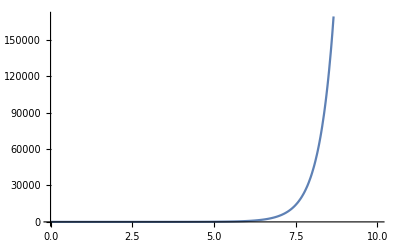

```mathematica
Plot[Gamma[1+x],{x,0,10}]
```

```mathematica
Solve[-1 == 2d - 2 d/α , α]
```

{{α→(2 d)/(1+2 d)}}

```mathematica
Solve[-1 == 2d - 2 d/α , d]
```

{{d→-α/(2 (-1+α))}}

```mathematica
FoxH[{{{a1,α1},…,{an,αn}},{{an+1,αn+1},…,{ap,αp}}},{{{b1,β1},…,{bm,βm}},{{bm+1,βm+1},…,{bq,βq}}},z]
```

FoxH[{{{a1,α1},…,{an,αn}},{{1+an,1+αn},…,{ap,αp}}},{{{b1,β1},…,{bm,βm}},{{1+bm,1+βm},…,{bq,βq}}},z]

```mathematica
FoxH[{{{1/2,1}},{{1/3,2}}},{{{1/4,3}},{{π,4}}},0.2]
```

0.0145499

```mathematica
FoxHReduce[Cos[ x],x]
```

1/2 √π FoxH[{{},{}},{{{0,1/2}},{{1/2,1/2}}},x/2]

```mathematica
FoxHlist=Inactivate[{Sequence[FoxH[{{},{}},{{{0,1}},{}},x],FoxH[{{},{}},{{{b,2}},{}},x],FoxH[{{{0,1}},{}},{{{0,1}},{{0,2/3}}},x],FoxH[{{{0,1}},{}},{{{0,1}},{{2,2/3}}},x],FoxH[{{},{}},{{{n/2,1/2}},{{-(n/2),1/2}}},x/2],FoxH[{{{1-a,1},{1-b,1}},{}},{{{0,1}},{{1-c,1}}},x],FoxH[{{{Subscript[a,1],1},{Subscript[a,2],1}},{{Subscript[a,3],1}}},{{{Subscript[b,1],1}},{{Subscript[b,2],1}}},x],FoxH[{{{Subscript[a,1],3},{Subscript[a,2],3}},{{Subscript[a,2],3}}},{{{Subscript[b,1],3}},{{Subscript[b,2],3}}},x]]},FoxH]
```

{FoxH[{{},{}},{{{0,1}},{}},x],FoxH[{{},{}},{{{b,2}},{}},x],FoxH[{{{0,1}},{}},{{{0,1}},{{0,2/3}}},x],FoxH[{{{0,1}},{}},{{{0,1}},{{2,2/3}}},x],FoxH[{{},{}},{{{n/2,1/2}},{{-n/2,1/2}}},x/2],FoxH[{{{1-a,1},{1-b,1}},{}},{{{0,1}},{{1-c,1}}},x],FoxH[{{{a_1,1},{a_2,1}},{{a_3,1}}},{{{b_1,1}},{{b_2,1}}},x],FoxH[{{{a_1,3},{a_2,3}},{{a_2,3}}},{{{b_1,3}},{{b_2,3}}},x]}

```mathematica
Grid[Sequence[Join[{{Text["FoxH with specific parameters"],Text["Simpler function"]}},Transpose[{ReplaceAll[Map[HoldForm,FoxHlist],Inactive[FoxH]->FoxH],Activate[FoxHlist]}]],Background->{None,{{None,GrayLevel[0.9]}},{{1,1}->Hue[0.6,0.4,1],{1,2}->Hue[0.6,0.4,1]}},BaseStyle->{FontFamily->Times,FontSize->12},Dividers->All,FrameStyle->Hue[0.6,0.4,0.8],Spacings->{2,1}]]//TraditionalForm
```

```mathematica
{{"FoxH with specific parameters", "Simpler function"}, {, ⅇ^-x}, {, 1/2 ⅇ^(-√x) x^(b/2)}, {, 2/3-x}, {, 2/3-1-x}, {, 2 nx}, {, a b abc-x}, {, Subscript[G, 3,2]^(1,2)(x|{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}, {Subscript[b, 1],Subscript[b, 2]}})}, {, 1/3 Subscript[G, 3,2]^(1,2)(x,3|{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 2]}, {Subscript[b, 1],Subscript[b, 2]}})}}J
```

```mathematica
Try the proof of Lemma 4.2 of Chen, Hu, Hu, Huang
```

```mathematica
1/2 √π FoxH[{{},{}},{{{0,1/2}},{{1/2,1/2}}},x/2]
```

```mathematica
Integrate[FoxH[{{{1,1/α}},{{Ceil[β],β}}},{{{1/2,α/2},{1,1}},{{1,α/2}}},x^α/(2^(α-1)ν t^β)] Cos[x ξ]/x,{x,0,∞},Assumptions->{0<β<2,α>0,t>0,ν>0,x>0,ξ>0}]
```

Integrate[(Cos[x ξ] FoxH[{{{1,1/α}},{{Ceil[β],β}}},{{{1/2,α/2},{1,1}},{{1,α/2}}},(2^(1-α) t^-β x^α)/ν])/x,{x,0,∞},Assumptions→{0<β<2,α>0,t>0,ν>0,x>0,ξ>0}]

```mathematica
A={{{{1,1/α}},{{Ceil[β],β}}},{{{1/2,α/2},{1,1}},{{1,α/2}}}}
```

{{{{1,1/α}},{{Ceil[β],β}}},{{{1/2,α/2},{1,1}},{{1,α/2}}}}

```mathematica
Length[A]
```

2

```mathematica
Length[A[[1]]]
```

2

```mathematica
A[[1]]
```

{{{1,1/α}},{{Ceil[β],β}}}

```mathematica
Param
```

```mathematica
Print[LockGauge[]]
```

LockGauge[]

```mathematica
StringForm["The value of x is ``.",5]
```

The value of x is 5.

```mathematica
Subscript[a, 1]
```

```mathematica
SuperStar[c]
```

```mathematica
Total[A]
```

Total[A]

```mathematica
Δ
```

```mathematica
Total[A[[1]][[1]]][[1]]
```

```mathematica
SuperStar[Subscript[a, 1]]
```

```mathematica
f[x_]:= x^x
```

```mathematica
Total[f/@A[[1]][[1]]]
```

{1,(1/α)^(1/α)}

```mathematica
Total[f/@A[[1]][[2]]]
```

{Ceil[β]^Ceil[β],β^β}

```mathematica
c = Total[f/@A[[2]][[1]]] Total[f/@A[[2]][[2]]]/Total[f/@A[[1]][[1]]]/Total[f/@A[[1]][[2]]]
```

{(1+1/(√2)) Ceil[β]^(-Ceil[β]),2^(-α/2) (1/α)^(-1/α) α^(α/2) (1+2^(-α/2) α^(α/2)) β^-β}

```mathematica
c[[1]]
```

(1+1/(√2)) Ceil[β]^(-Ceil[β])

```mathematica
c[[2]]
```

2^(-α/2) (1/α)^(-1/α) α^(α/2) (1+2^(-α/2) α^(α/2)) β^-β

```mathematica
( Total[f/@A[[2]][[1]]] Total[f/@A[[2]][[2]]]/Total[f/@A[[1]][[1]]]/Total[f/@A[[1]][[2]]])[[2]]//FullSimplify
```

2^-α (1/α)^(-1/α) (2^(α/2) α^(α/2)+α^α) β^-β

```mathematica
m=1
```

1

```mathematica
bjl=Table[Table[(-A[[1]][[1]][[i]][[1]]-l)/A[[1]][[1]][[i]][[2]],{i,1,m}],{l,0,10}]
```

{{-α},{-2 α},{-3 α},{-4 α},{-5 α},{-6 α},{-7 α},{-8 α},{-9 α},{-10 α},{-11 α}}

```mathematica
A[[1]][[1]][[1]][[2]]
```

1/α

```mathematica
m
```

m

```mathematica
A[[2]][[1]]
```

{{1/2,α/2},{1,1}}

```mathematica
m=2
Min[Table[A[[2]][[1]][[j]][[1]]/A[[2]][[1]][[j]][[2]],{j,1,m}]]
```

2

Min[1,1/α]